```mathematica
usaqis={0,51,101,151,201,301,401,500};
uspm25s=N@{0,12.1,35.5,55.5,150.5,250.5,350.5,500.4};
```

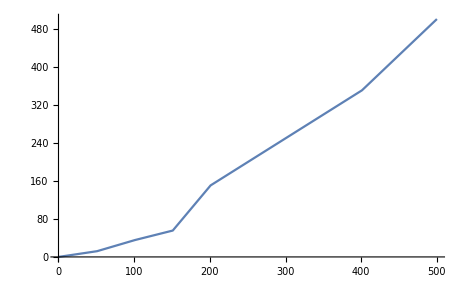

```mathematica
ListLinePlot[{usaqis[[#]],uspm25s[[#]]}&/@Range@Length@usaqis]
```

```mathematica
baqis={{100,79,59,39,19,0},{0,13,25,45,110,500}}
```

{{100,79,59,39,19,0},{0,13,25,45,110,500}}

```mathematica
usAQI=Interpolation[{uspm25s[[#]],usaqis[[#]]}&/@Range@Length@usaqis,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
usAQI/@baqis[[2]]
```

{7.10543×10^-15,52.9231,78.5641,124.75,179.684,499.736}

```mathematica
usAQI[150]
```

200.737

```mathematica
usAQI[10]
```

42.1488

```mathematica
usAQI[110+.1(500-110)]
```

200.211

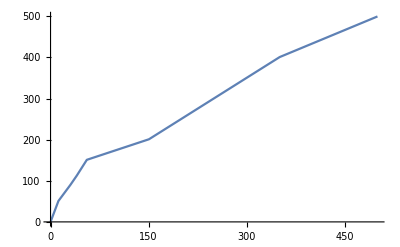

```mathematica
Plot[usAQI[x],{x,0,500}]
```

```mathematica
usAQI/@{160.,115.,80.}
```

{210.5,182.316,163.895}

```mathematica
usAQI[65.]
```

156.

```mathematica
usAQI[27]
```

82.8376